# Multi-state diabatization for 1D system

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/souda/Documents/Projects/Multistate-diabatization/models

## 3-state model

### Diabatic potentials

```mathematica
x1=-1;
x2=1;
x3=1;
Δ1=0;
Δ2=0;
Δ3=1;
```

```mathematica
U1[x_]:=1/2(x-x1)^2+Δ1;
U2[x_]:=1/2(x-x2)^2+Δ2;
U3[x_]:=1/2(x-x3)^2+Δ3;
```

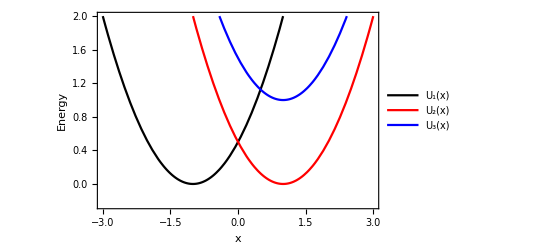

```mathematica
Plot[{U1[x],U2[x],U3[x]},{x,-3,3},
PlotRange->{-0.25,2},Frame->True,
PlotStyle->{Black,Red,Blue},
BaseStyle->{FontSize->12},
FrameLabel->{x,"Energy"},
PlotLegends->{"U_1(x)","U_2(x)","U_3(x)"}]
```

### Crossing points

```mathematica
xp12=Solve[U1[x]==U2[x],x]⟦1,1,2⟧
```

0

```mathematica
xp13=Solve[U1[x]==U3[x],x]⟦1,1,2⟧
```

1/2

### Diabatic couplings

```mathematica
V12=0.1;
V13=0.1;
V23=0;
```

### Hamiltonian in the original diabatic basis

```mathematica
H[x_]:=({{U1[x], V12, V13}, {V12, U2[x], V23}, {V13, V13, U3[x]}});
```

```mathematica
H[x]//MatrixForm
```

(1/2 (1+x)^2 | 0.1 | 0.1
0.1 | 1/2 (-1+x)^2 | 0
0.1 | 0.1 | 1+1/2 (-1+x)^2)

### Adiabatic energy surfaces

```mathematica
E1[x_]:=Reverse[Eigenvalues[N[H[x]]]]⟦1⟧;
E2[x_]:=Reverse[Eigenvalues[N[H[x]]]]⟦2⟧;
E3[x_]:=Reverse[Eigenvalues[N[H[x]]]]⟦3⟧;
```

```mathematica
C1[x_]:=Reverse[Eigenvectors[N[H[x]]]]⟦1⟧;
C2[x_]:=Reverse[Eigenvectors[N[H[x]]]]⟦2⟧;
C3[x_]:=Reverse[Eigenvectors[N[H[x]]]]⟦3⟧;
```

```mathematica
c1[x_]:=(2HeavisideTheta[C1[x].C1[0]]-1)C1[x];
c2[x_]:=(2HeavisideTheta[C2[x].C2[0]]-1)C2[x];
c3[x_]:=(2HeavisideTheta[C3[x].C3[0]]-1)C3[x];
```

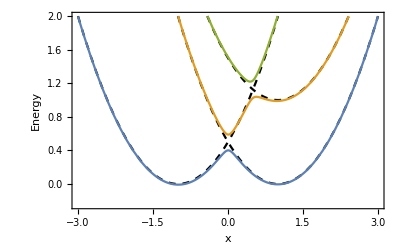

```mathematica
Show[
Plot[{U1[x],U2[x],U3[x]},{x,-3,3},PlotRange->{-0.25,2},PlotStyle->{{Black,Dashed}}],
Plot[{E1[x],E2[x],E3[x]},{x,-3,3},PlotRange->{-0.25,2}],
Frame->True,FrameLabel->{"x","Energy"},
GridLines->{{xp12,xp13},None},GridLinesStyle->Directive[Gray,Dashed],
BaseStyle->{FontSize->12}
]
```

### Derivative couplings between adiabatic states

```mathematica
d12[x_]:=(c1[x]⟦1⟧c2[x]⟦1⟧(x-x1)+c1[x]⟦2⟧c2[x]⟦2⟧(x-x2)+c1[x]⟦3⟧c2[x]⟦3⟧(x-x3))/(E2[x]-E1[x]);
d13[x_]:=(c1[x]⟦1⟧c3[x]⟦1⟧(x-x1)+c1[x]⟦2⟧c3[x]⟦2⟧(x-x2)+c1[x]⟦3⟧c3[x]⟦3⟧(x-x3))/(E3[x]-E1[x]);
d23[x_]:=(c2[x]⟦1⟧c3[x]⟦1⟧(x-x1)+c2[x]⟦2⟧c3[x]⟦2⟧(x-x2)+c2[x]⟦3⟧c3[x]⟦3⟧(x-x3))/(E3[x]-E2[x]);
```

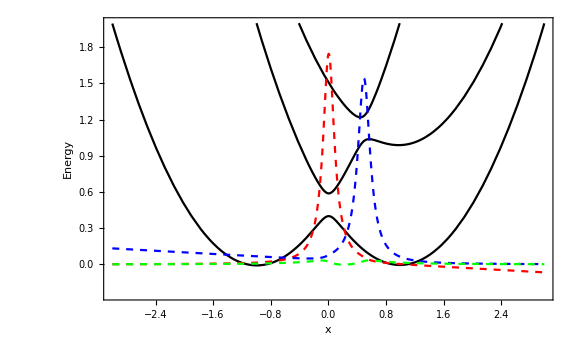

```mathematica
Plot[{E1[x],E2[x],E3[x],1/3 d12[x],1/3 d23[x],1/3 d13[x]},{x,-3,3},
Axes->True,Frame->True,
FrameLabel->{"x","Energy",None,"Derivative coupling"},
PlotRange->{-0.25,2},
PlotStyle->{Black,Black,Black,{Red,Dashed},{Blue,Dashed},{Green,Dashed}},
GridLines->{{xp12,xp13},None},GridLinesStyle->Directive[Gray,Dashed],
BaseStyle->{FontSize->14},
ImageSize->Large]
```

```mathematica
d[x_]:=({{0, d12[x], d13[x]}, {-d12[x], 0, d23[x]}, {-d13[x], -d23[x], 0}});
```

```mathematica
Clear[τ]
```

```mathematica
τ:=({{0, τ12, τ13}, {-τ12, 0, τ23}, {-τ13, -τ23, 0}});
```

```mathematica
τ//MatrixForm
```

(0 | τ12 | τ13
-τ12 | 0 | τ23
-τ13 | -τ23 | 0)

### General (orthogonal) adiabatic to diabatic transformation (ADT) matrix

```mathematica
RotationMatrix[θ,{0,0,1}]//MatrixForm
```

(Cos[θ] | -Sin[θ] | 0
Sin[θ] | Cos[θ] | 0
0 | 0 | 1)

```mathematica
A[x_]:=RotationMatrix[θ23[x],{1,0,0}].RotationMatrix[θ13[x],{0,1,0}].RotationMatrix[θ12[x],{0,0,1}];
```

```mathematica
A[x]//MatrixForm
```

(Cos[θ12[x]] Cos[θ13[x]] | -Cos[θ13[x]] Sin[θ12[x]] | Sin[θ13[x]]
Cos[θ23[x]] Sin[θ12[x]]+Cos[θ12[x]] Sin[θ13[x]] Sin[θ23[x]] | Cos[θ12[x]] Cos[θ23[x]]-Sin[θ12[x]] Sin[θ13[x]] Sin[θ23[x]] | -Cos[θ13[x]] Sin[θ23[x]]
-Cos[θ12[x]] Cos[θ23[x]] Sin[θ13[x]]+Sin[θ12[x]] Sin[θ23[x]] | Cos[θ23[x]] Sin[θ12[x]] Sin[θ13[x]]+Cos[θ12[x]] Sin[θ23[x]] | Cos[θ13[x]] Cos[θ23[x]])

### Differential equations for ADT matrix elements

```mathematica
D[A[x],x]//MatrixForm
```

(-Cos[θ13[x]] Sin[θ12[x]] θ12'[x]-Cos[θ12[x]] Sin[θ13[x]] θ13'[x] | -Cos[θ12[x]] Cos[θ13[x]] θ12'[x]+Sin[θ12[x]] Sin[θ13[x]] θ13'[x] | Cos[θ13[x]] θ13'[x]
Cos[θ12[x]] Cos[θ23[x]] θ12'[x]-Sin[θ12[x]] Sin[θ13[x]] Sin[θ23[x]] θ12'[x]+Cos[θ12[x]] Cos[θ13[x]] Sin[θ23[x]] θ13'[x]+Cos[θ12[x]] Cos[θ23[x]] Sin[θ13[x]] θ23'[x]-Sin[θ12[x]] Sin[θ23[x]] θ23'[x] | -Cos[θ23[x]] Sin[θ12[x]] θ12'[x]-Cos[θ12[x]] Sin[θ13[x]] Sin[θ23[x]] θ12'[x]-Cos[θ13[x]] Sin[θ12[x]] Sin[θ23[x]] θ13'[x]-Cos[θ23[x]] Sin[θ12[x]] Sin[θ13[x]] θ23'[x]-Cos[θ12[x]] Sin[θ23[x]] θ23'[x] | Sin[θ13[x]] Sin[θ23[x]] θ13'[x]-Cos[θ13[x]] Cos[θ23[x]] θ23'[x]
Cos[θ23[x]] Sin[θ12[x]] Sin[θ13[x]] θ12'[x]+Cos[θ12[x]] Sin[θ23[x]] θ12'[x]-Cos[θ12[x]] Cos[θ13[x]] Cos[θ23[x]] θ13'[x]+Cos[θ23[x]] Sin[θ12[x]] θ23'[x]+Cos[θ12[x]] Sin[θ13[x]] Sin[θ23[x]] θ23'[x] | Cos[θ12[x]] Cos[θ23[x]] Sin[θ13[x]] θ12'[x]-Sin[θ12[x]] Sin[θ23[x]] θ12'[x]+Cos[θ13[x]] Cos[θ23[x]] Sin[θ12[x]] θ13'[x]+Cos[θ12[x]] Cos[θ23[x]] θ23'[x]-Sin[θ12[x]] Sin[θ13[x]] Sin[θ23[x]] θ23'[x] | -Cos[θ23[x]] Sin[θ13[x]] θ13'[x]-Cos[θ13[x]] Sin[θ23[x]] θ23'[x])

```mathematica
dA[x_]:=D[A[x],x];
```

```mathematica
dA[x]⟦1,1⟧
```

-Cos[θ13[x]] Sin[θ12[x]] θ12'[x]-Cos[θ12[x]] Sin[θ13[x]] θ13'[x]

```mathematica
LHS[x]:=dA[x]+τ.A[x];
```

```mathematica
Part[LHS[x],1,1]==0
```

τ13 (-Cos[θ12[x]] Cos[θ23[x]] Sin[θ13[x]]+Sin[θ12[x]] Sin[θ23[x]])+τ12 (Cos[θ23[x]] Sin[θ12[x]]+Cos[θ12[x]] Sin[θ13[x]] Sin[θ23[x]])-Cos[θ13[x]] Sin[θ12[x]] θ12'[x]-Cos[θ12[x]] Sin[θ13[x]] θ13'[x]==0

```mathematica
LHS[x]⟦1,2⟧==0
```

τ13 (Cos[θ23[x]] Sin[θ12[x]] Sin[θ13[x]]+Cos[θ12[x]] Sin[θ23[x]])+τ12 (Cos[θ12[x]] Cos[θ23[x]]-Sin[θ12[x]] Sin[θ13[x]] Sin[θ23[x]])-Cos[θ12[x]] Cos[θ13[x]] θ12'[x]+Sin[θ12[x]] Sin[θ13[x]] θ13'[x]==0

```mathematica
Flatten@Table[i*10+j,{i,1,3},{j,i+1,3}]
```

{12,13,23}

```mathematica
deqs9=Flatten[Table[Part[LHS[x],i,j]==0,{i,1,3},{j,1,3}]];
```

```mathematica
deqs9//FullSimplify//TableForm//TraditionalForm
```

sin(θ12(x)) (τ12 cos(θ23(x))+τ13 sin(θ23(x)))==θ12'(x) sin(θ12(x)) cos(θ13(x))+cos(θ12(x)) sin(θ13(x)) (θ13'(x)-τ12 sin(θ23(x))+τ13 cos(θ23(x)))
sin(θ12(x)) sin(θ13(x)) (θ13'(x)-τ12 sin(θ23(x))+τ13 cos(θ23(x)))+cos(θ12(x)) (τ12 cos(θ23(x))+τ13 sin(θ23(x)))==θ12'(x) cos(θ12(x)) cos(θ13(x))
cos(θ13(x)) (θ13'(x)-τ12 sin(θ23(x))+τ13 cos(θ23(x)))==0
sin(θ12(x)) sin(θ23(x)) (-τ23+θ12'(x) sin(θ13(x))+θ23'(x))+τ12 cos(θ12(x)) cos(θ13(x))==cos(θ12(x)) (cos(θ23(x)) (θ12'(x)+sin(θ13(x)) (θ23'(x)-τ23))+θ13'(x) cos(θ13(x)) sin(θ23(x)))
sin(θ12(x)) sin(θ13(x)) cos(θ23(x)) (τ23-θ23'(x))+τ12 sin(θ12(x)) cos(θ13(x))+cos(θ12(x)) sin(θ23(x)) (τ23-θ23'(x))==θ12'(x) (cos(θ12(x)) sin(θ13(x)) sin(θ23(x))+sin(θ12(x)) cos(θ23(x)))+sin(θ12(x)) θ13'(x) cos(θ13(x)) sin(θ23(x))
cos(θ13(x)) cos(θ23(x)) (θ23'(x)-τ23)+τ12 sin(θ13(x))==θ13'(x) sin(θ13(x)) sin(θ23(x))
cos(θ12(x)) θ13'(x) cos(θ13(x)) cos(θ23(x))+cos(θ12(x)) sin(θ13(x)) sin(θ23(x)) (τ23-θ23'(x))+τ13 cos(θ12(x)) cos(θ13(x))+sin(θ12(x)) cos(θ23(x)) (τ23-θ23'(x))==θ12'(x) (sin(θ12(x)) sin(θ13(x)) cos(θ23(x))+cos(θ12(x)) sin(θ23(x)))
θ12'(x) (sin(θ12(x)) sin(θ23(x))-cos(θ12(x)) sin(θ13(x)) cos(θ23(x)))+(τ23-θ23'(x)) (cos(θ12(x)) cos(θ23(x))-sin(θ12(x)) sin(θ13(x)) sin(θ23(x)))==sin(θ12(x)) cos(θ13(x)) (τ13+θ13'(x) cos(θ23(x)))
cos(θ13(x)) sin(θ23(x)) (τ23-θ23'(x))==sin(θ13(x)) (τ13+θ13'(x) cos(θ23(x)))

```mathematica
deqs3=Flatten[Table[LHS[x]⟦i,i⟧==0,{i,1,3}]]
```

{τ13 (-Cos[θ12[x]] Cos[θ23[x]] Sin[θ13[x]]+Sin[θ12[x]] Sin[θ23[x]])+τ12 (Cos[θ23[x]] Sin[θ12[x]]+Cos[θ12[x]] Sin[θ13[x]] Sin[θ23[x]])-Cos[θ13[x]] Sin[θ12[x]] θ12'[x]-Cos[θ12[x]] Sin[θ13[x]] θ13'[x]==0,τ12 Cos[θ13[x]] Sin[θ12[x]]+τ23 (Cos[θ23[x]] Sin[θ12[x]] Sin[θ13[x]]+Cos[θ12[x]] Sin[θ23[x]])-Cos[θ23[x]] Sin[θ12[x]] θ12'[x]-Cos[θ12[x]] Sin[θ13[x]] Sin[θ23[x]] θ12'[x]-Cos[θ13[x]] Sin[θ12[x]] Sin[θ23[x]] θ13'[x]-Cos[θ23[x]] Sin[θ12[x]] Sin[θ13[x]] θ23'[x]-Cos[θ12[x]] Sin[θ23[x]] θ23'[x]==0,-τ13 Sin[θ13[x]]+τ23 Cos[θ13[x]] Sin[θ23[x]]-Cos[θ23[x]] Sin[θ13[x]] θ13'[x]-Cos[θ13[x]] Sin[θ23[x]] θ23'[x]==0}

```mathematica
initcond12={θ12[xp12]==π/4,θ13[xp12]==0,θ23[xp12]==0};
initcond13={θ13[xp13]==π/4,θ12[xp13]==0,θ23[xp13]==0};
```

```mathematica
deqs3init12=Join[deqs3,initcond12]
```

{(Cos[θ23[x]] Sin[θ12[x]]+Cos[θ12[x]] Sin[θ13[x]] Sin[θ23[x]]) τ12[x]+(-Cos[θ12[x]] Cos[θ23[x]] Sin[θ13[x]]+Sin[θ12[x]] Sin[θ23[x]]) τ13[x]-Cos[θ13[x]] Sin[θ12[x]] θ12'[x]-Cos[θ12[x]] Sin[θ13[x]] θ13'[x]==0,Cos[θ13[x]] Sin[θ12[x]] τ12[x]+(Cos[θ23[x]] Sin[θ12[x]] Sin[θ13[x]]+Cos[θ12[x]] Sin[θ23[x]]) τ23[x]-Cos[θ23[x]] Sin[θ12[x]] θ12'[x]-Cos[θ12[x]] Sin[θ13[x]] Sin[θ23[x]] θ12'[x]-Cos[θ13[x]] Sin[θ12[x]] Sin[θ23[x]] θ13'[x]-Cos[θ23[x]] Sin[θ12[x]] Sin[θ13[x]] θ23'[x]-Cos[θ12[x]] Sin[θ23[x]] θ23'[x]==0,-Sin[θ13[x]] τ13[x]+Cos[θ13[x]] Sin[θ23[x]] τ23[x]-Cos[θ23[x]] Sin[θ13[x]] θ13'[x]-Cos[θ13[x]] Sin[θ23[x]] θ23'[x]==0,θ12[0]==π/4,θ13[0]==0,θ23[0]==0}

```mathematica
d[0]
```

{{0,5.21916,0.0695177},{-5.21916,0,0.228252},{-0.0695177,-0.228252,0}}

```mathematica
deqs3init12={(Cos[θ23[x]] Sin[θ12[x]]+Cos[θ12[x]] Sin[θ13[x]] Sin[θ23[x]]) d12[x]+(-Cos[θ12[x]] Cos[θ23[x]] Sin[θ13[x]]+Sin[θ12[x]] Sin[θ23[x]]) d13[x]-Cos[θ13[x]] Sin[θ12[x]] θ12'[x]-Cos[θ12[x]] Sin[θ13[x]] θ13'[x]==0,Cos[θ13[x]] Sin[θ12[x]] d12[x]+(Cos[θ23[x]] Sin[θ12[x]] Sin[θ13[x]]+Cos[θ12[x]] Sin[θ23[x]]) d23[x]-Cos[θ23[x]] Sin[θ12[x]] θ12'[x]-Cos[θ12[x]] Sin[θ13[x]] Sin[θ23[x]] θ12'[x]-Cos[θ13[x]] Sin[θ12[x]] Sin[θ23[x]] θ13'[x]-Cos[θ23[x]] Sin[θ12[x]] Sin[θ13[x]] θ23'[x]-Cos[θ12[x]] Sin[θ23[x]] θ23'[x]==0,-Sin[θ13[x]] d13[x]+Cos[θ13[x]] Sin[θ23[x]] d23[x]-Cos[θ23[x]] Sin[θ13[x]] θ13'[x]-Cos[θ13[x]] Sin[θ23[x]] θ23'[x]==0,θ12[0]==-π/4,θ13[0]==0,θ23[0]==0};
```

```mathematica
solution=NDSolve[deqs3init12,{θ12,θ13,θ23},{x,-5,5},Method->{"EquationSimplification"->"Residual"}]
```

{{θ12→InterpolatingFunction[…],θ13→InterpolatingFunction[…],θ23→InterpolatingFunction[…]}}

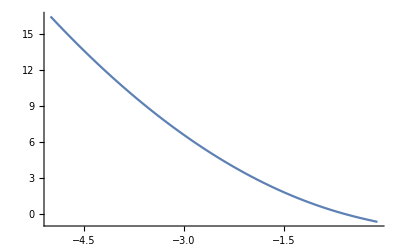

```mathematica
Plot[Evaluate[θ12[x]/.solution],{x,-5,-0.1},PlotRange->All]
```